```mathematica
(4.17/10)^-1*20
```

47.9616

```mathematica
48*5/6
```

40

```mathematica
40*5/4.
```

50.

```mathematica
0.1*50
```

5.

```mathematica
((3.25+3+3)/4)/3
```

0.770833

```mathematica
40/0.8
```

50.

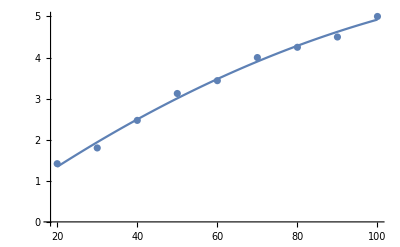

0.0157003+0.0705877 x-0.000215076 x^2

```mathematica
speed = {2,3,4,5,6,7,8,9,10}*10;
overshoot= {
(*20*){2,2,1,2,1,2,1,1,1,1,2,1},
(*30*){3,2,1,3,1,3,1,1,1,1,2,2,2,2,2},
(*40*){2,2,3,2,2,3,3,1,3,3,3,2,3,2,2,3,3},
(*50*){3,3,4,3,2,4,2,2,4,2,3,3,3,4,3,5},
(*60*){4,3,3,3,3,3,3,3,3,3,4,4,4,3,4,5},
(*70*){4(*3,3,4,3,4,5,5,4,4,5,4,5,4,5,5,5,5,6*)},
(*80*){4.25(*5,4,6,6,5,4,4,5,5,5,4,5,5,5,6,5,6,5,5,5,6*)},
(*90*){4.5(*6,6,6,5,5,4,4,6,5,5,4,4,5,5,4,5,5*)},
(*100*){5(*6,5,8,6,6,7,8,8,6,8,6,5,7,8,6,5,7,5,6,7,6,8,6*)}
};

overshootavg = Table[{},9];
For[i=1,i<10,i++,
overshootavg[[i]] = Total[overshoot[[i]]]/Length[overshoot[[i]]];
];

funct[x_]=Fit[Transpose[{speed,overshootavg}],{1,x,x^2},x];
Show[
ListPlot[Transpose[{speed,overshootavg}]],
Plot[funct[x],{x,20,100}]
]
funct[x]
```

```mathematica
funct[x]
```

0.695302+0.267472 x

```mathematica
Total[{27,27,29,27,27,27}]/6.
```

27.3333

-11.8876+0.372714 x+0.00207748 x^2

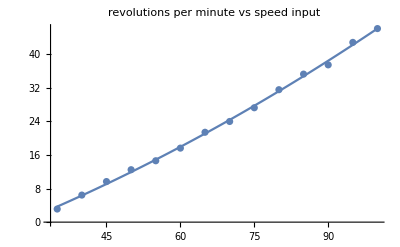

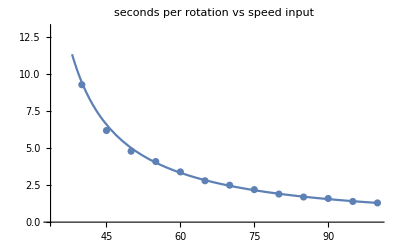

```mathematica
speed = Table[35+i,{i,0,100-35,5}];
spr = {19.2,9.3,6.2,4.8,4.1,3.4,2.8,2.5,2.2,1.9,1.7,1.6,1.4,1.3};
rpm = 1/spr*60;
data = Transpose[{speed,rpm}];
funcRPM[x_]=Fit[data,{1,x,x^2},x]
Show[
ListPlot[data,PlotLabel->"revolutions per minute vs speed input"],
Plot[funcRPM[x],{x,35,100}]
]

funcSPR[x_] = 60/funcRPM[x];
Show[
ListPlot[ Transpose[{speed,spr}],PlotLabel->"seconds per rotation vs speed input"],
Plot[funcSPR[x],{x,35,100}]
]
```

```mathematica
Solve[r == 1/s*60,s]
```

{{s→60/r}}

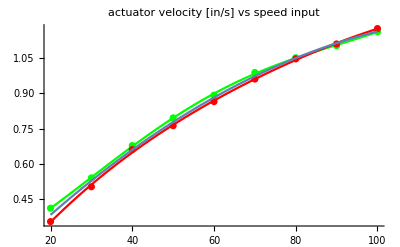

0.054397+0.0178693 x-0.0000678376 x^2

```mathematica
speed = Table[i,{i,20,100,10}];
t2mEXTEND = {
(*20*){2.452,2.352,2.402,2.352,2.402,2.402,2.402,2.452,2.452,2.552},
(*30*){1.852,1.802,1.802,1.851,1.802,1.851,1.852,1.852,1.901,1.902},
(*40*){1.502,1.451,1.451,1.452,1.452,1.474,1.451,1.501,1.502,1.502},
(*50*){1.251,1.251,1.251,1.251,1.252,1.252,1.251,1.251,1.251,1.301},
(*60*){1.101,1.101,1.101,1.101,1.101,1.101,1.151,1.151,1.151,1.151},
(*70*){1.001,1.001,1.001,1.001,1.001,1.001,1.001,1.01,1.051,1.051},
(*80*){0.951,0.951,0.951,0.951,0.951,0.9530001,0.951,0.951,0.951},
(*90*){0.9120001,0.906,0.901,0.901,0.901,0.9080001,0.929,0.901,0.906},
(*100*){0.8610001,0.8710001,0.851,0.9030001,0.851,0.851,0.851,0.851}
};
t2mRETRACT= {
(*20*){3.152,3.002,2.902,2.802,2.702,2.702,2.652,2.702,2.702,2.752,2.902},
(*30*){2.151,2.051,2.001,2.002,1.952,1.952,1.951,1.902,1.952,1.951},
(*40*){1.602,1.551,1.501,1.462,1.501,1.501,1.501,1.502,1.502,1.462,1.551},
(*50*){1.351,1.351,1.301,1.301,1.301,1.301,1.301,1.301,1.301,1.301},
(*60*){1.201,1.151,1.151,1.151,1.151,1.151,1.151,1.151,1.151,1.151},
(*70*){1.051,1.051,1.051,1.051,1.051,1.001,1.051,1.001,1.051,1.051},
(*80*){1.001,0.951,0.951,0.95,0.951,0.951,0.951,0.951,0.951,0.951},
(*90*){0.901,0.901,0.901,0.901,0.901,0.901,0.901,0.901,0.901,0.901},
(*100*){0.851,0.851,0.851,0.851,0.851,0.851,0.851,0.851,0.851,0.851}
};

t2mEXTEND= 1/t2mEXTEND;
t2mRETRACT= 1/t2mRETRACT;

t2mEXTENDavg = Table[{},9];
t2mRETRACTavg = Table[{},9];
For[i=1,i<10,i++,
t2mEXTENDavg[[i]] = Total[t2mEXTEND[[i]]]/Length[t2mEXTEND[[i]]];
t2mRETRACTavg[[i]]=Total[t2mRETRACT[[i]]]/Length[t2mRETRACT[[i]]];
];
functRetract[x_]=Fit[Transpose[{speed,t2mRETRACTavg}],{1,x,x^2,x^3,x^4},x];
functExtend[x_]=Fit[Transpose[{speed,t2mEXTENDavg}],{1,x,x^2,x^3,x^4},x];
functAvg[x_]=Fit[Join[Transpose[{speed,t2mRETRACTavg}],Transpose[{speed,t2mEXTENDavg}]],{1,x,x^2},x];
Show[
ListPlot[Transpose[{speed,t2mEXTENDavg}],PlotStyle->Green,PlotLabel->"actuator velocity [in/s] vs speed input"],
Plot[functExtend[x],{x,20,100},PlotStyle->Green],
ListPlot[Transpose[{speed,t2mRETRACTavg}],PlotStyle->Red],
Plot[functRetract[x],{x,20,100},PlotStyle->Red],
Plot[functAvg[x],{x,20,100}],
PlotRange->All
]
functAvg[x]
```

```mathematica
distance/velocity == 0.75(seconds per revolution)
```

```mathematica
rootFun[actSpeed_,winchSpeed_,x_]:=x/functAvg[actSpeed]-0.33*funcSPR[winchSpeed]; (*positive if too slow, negative if too fast*)
err = 1;
iterations = 0;

dist = 0.375;
winchSpeed =100;
x0 = 38;
x1 = 38+1;

maxActTime= dist/functAvg[20];
minActTime = dist/functAvg[100];
Print["goal time: ",0.33*funcSPR[winchSpeed]];
Print["max time :",maxActTime];
Print["min time :",minActTime];

If[rootFun[20,winchSpeed,dist]<0,x2 = 20;iterations=1000;Print["min speed"]];
If[rootFun[100,winchSpeed,dist]>0, x2 = 100;iterations=1000;Print["max speed"]];

While[err > 10^-3 && iterations < 10,
x2=x1- rootFun[x1,winchSpeed,dist]*(x1-x0)/(rootFun[x1,winchSpeed,dist]-rootFun[x0,winchSpeed,dist]);
err = Abs[rootFun[x2,winchSpeed,dist]];
x0=x1;
x1=x2;
iterations++;
Print[iterations];
Print["   Guess: ",x2];
Print["   remainder: ",err];
]
Print[x2]
```

goal time: 0.428956

max time :0.974915

min time :0.322454

1

Guess: 51.9964

remainder: 0.0397171

2

Guess: 56.6922

remainder: 0.0125219

3

Guess: 58.8544

remainder: 0.00153007

4

Guess: 59.1553

remainder: 0.0000679319

59.1553

```mathematica
functAvg[in]
```

0.054397+0.0178693 in-0.0000678376 in^2

```mathematica
Solve[χ/(¢_0+¢_1*P+¢_2*P^2)*()==τ,P]
```

{{P→(-τ ¢_1+√(τ^2 ¢_1^2+4 τ χ ¢_2-4 τ^2 ¢_0 ¢_2))/(2 τ ¢_2)},{P→-(τ ¢_1+√(τ^2 ¢_1^2+4 τ χ ¢_2-4 τ^2 ¢_0 ¢_2))/(2 τ ¢_2)}}

```mathematica
winchSpeed=100;
τ=0.33*funcSPR[winchSpeed];
¢_0 = 0.054397;
¢_1 = 0.0178693;
¢_2 = -0.0000678376;
χ = 0.375;

(-τ ¢_1+√(τ^2 ¢_1^2+4 τ χ ¢_2-4 τ^2 ¢_0 ¢_2))/(2 τ ¢_2)
```

59.1697